```mathematica
PrePostAppend0[list_]:={0}~Join~list~Join~{0}
PrePostAppendEnlarge[list_]:={First[list]}~Join~list~Join~{Last[list]}
render3DField[e_,xe_,h_,xh_]:=Graphics3D[{
Black,
Line[{{0,Min[xe],0},{0,Max[xe],0}}],
Opacity[0.5,Blue],Thick,
Polygon[Transpose[{ConstantArray[0,Length[xe]+2],PrePostAppendEnlarge@xe,PrePostAppend0[e]}]],
Opacity[0.5,Red],
Polygon[Transpose[{PrePostAppend0[h],PrePostAppendEnlarge@xh,ConstantArray[0,Length[xh]+2]}]]
},PlotRange->{{-1.5,1.5},MinMax[xe],{-1.5,1.5}},BoxRatios->{1,5,1},ImageSize->{500,200},ViewPoint->{1.3,-0.5,1}]
```

## A2b

```mathematica
raw=Import[FileNameJoin[{NotebookDirectory[],"A2b.csv"}]];
```

```mathematica
snapshots=raw[[1]];
xe=raw[[2]];
xh=raw[[3]];
efields=raw[[3+#]]&/@Range[Length[snapshots]];
hfields=raw[[3+Length[snapshots]+#]]&/@Range[Length[snapshots]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"A2b_Start.png"}],render3DField[efields[[1]],xe,hfields[[1]],xh]]
Export[FileNameJoin[{NotebookDirectory[],"A2b_End.png"}],render3DField[efields[[-1]],xe,hfields[[-1]],xh]]
```

C:\Users\Jelle\Desktop\coding\ComputationalPhotonics\Excercise_02\A2\A2b_Start.png

C:\Users\Jelle\Desktop\coding\ComputationalPhotonics\Excercise_02\A2\A2b_End.png

```mathematica
crash=render3DField[efields[[#]],xe,hfields[[#]],xh]&/@Range[13,17];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"A2b_Crash_"<>ToString[#]<>".png"}],crash[[#]]]&/@Range[Length@crash];
```

## A2c

```mathematica
raw=Import[FileNameJoin[{NotebookDirectory[],"A2c.csv"}]];
```

```mathematica
snapshots=raw[[1]];
xe=raw[[2]];
xh=raw[[3]];
efields=raw[[3+#]]&/@Range[Length[snapshots]];
hfields=raw[[3+Length[snapshots]+#]]&/@Range[Length[snapshots]];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"A2c.png"}],render3DField[efields[[1]],xe,hfields[[1]],xh]]
```

C:\Users\Jelle\Desktop\coding\ComputationalPhotonics\Excercise_02\A2\A2c.png

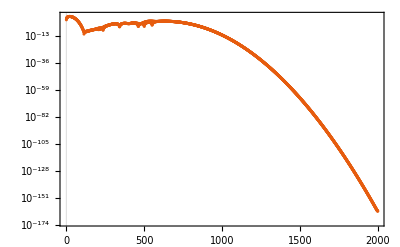

```mathematica
ListLogPlot[hfields[[1]]^2,PlotRange->All]
```

## A2f

```mathematica
raw=Import[FileNameJoin[{NotebookDirectory[],"A2f.csv"}]];
```

```mathematica
snapshots=raw[[1]];
xe=raw[[2]];
xh=raw[[3]];
efields=raw[[3+#]]&/@Range[Length[snapshots]];
hfields=raw[[3+Length[snapshots]+#]]&/@Range[Length[snapshots]];
```

```mathematica
transition=render3DField[efields[[#]],xe,hfields[[#]],xh]&/@Range[12,16];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"A2f_Transition_"<>ToString[#]<>".png"}],transition[[#]]]&/@Range[Length@transition];
```